# Circuit polynomials in the Cayley-Manger ideal - Instructions

## Importing a .wdx file

Circuit polynomials are saved as a compressed .wdx file and have to be imported into a notebook via the Import function. To import a .wdx file, save it to disk and import as poly=Import[“file path”]; where file path is the full  path of the .wdx file. Mathematica V12.0 (and possibly earlier versions) will offer a file browser in the drop-down menu when Import is typed.

If a .wdx file is saved in Mathematica’s current working directory, it can be imported simply with poly=Import[filename.wdx].
To check the location of Mathematica’s current working directory, evaluate the following cell:

```mathematica
Directory[]
```

To set the location of the current working directory, evaluate SetDirectory[“directory path”]. As with Import, typing SetDirectory will prompt a drop-down menu that offers a directory browser.

## Example: the Desargues-plus-one circuit polynomial

```mathematica
SetDirectory["C:\\Users\\goran\\Desktop\\Mathematica Working Folder"]
```

C:\Users\goran\Desktop\Mathematica Working Folder

Assuming that desarguesPlusOne.wdx is saved in the current working directory, we import it with the Import function. We recommend to suppress the output since circuit polynomials have a large number of terms .

```mathematica
desarguesPlusOne=Import["desarguesPlusOne.wdx"];
```

We can now gather some information about the circuit polynomial of the Desargues-plus-one circuit

```mathematica
support=Variables[desarguesPlusOne]
exponents=Exponent[desarguesPlusOne,#]&/@support
homDegree=Total[Exponent[desarguesPlusOne[[1]],#]&/@support]
numbTerms=Length[desarguesPlusOne]
irreducible=IrreduciblePolynomialQ[desarguesPlusOne]
```

{x_(1,2),x_(1,4),x_(1,5),x_(2,3),x_(2,5),x_(3,4),x_(2,6),x_(3,6),x_(4,5),x_(5,6)}

{8,8,8,8,12,8,8,8,8,8}

20

658175

True

## Drawing and Vertex Relabelling

### Drawing the sparsity circuit corresponding to a circut polynomial

The following function takes a circuit polynomial as input and returns its corresponding sparsity circuit.

```mathematica
polyToGraph[poly_]:=Module[
{support,edges,i},
support=Variables[poly];
edges=Table[support[[i,2]]->support[[i,3]],{i,1,Length[support]}];
GraphComputation`GraphPlotLegacy[edges,VertexLabeling->True]
]
```

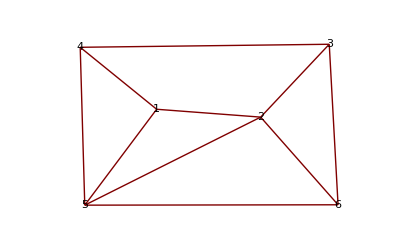

### Relabelling vertices

If we want to use the circuit polynomial of the Desargues-plus-one circuit with a different set of labels, we can use the vertexSub function below to relabel the indeterminates.

The function vertexSub takes as input:
	a circuit polynomial, and
	a list of the form {a->b,c->d,...} where i->j indicates that the vertex i is to be relabeled into j. If for a vertex i there is no replacement instruction, then no relabelling occurs at i. 
This function returns the circuit polynomial of the relabeled sparsity circuit.

```mathematica
vertexSub[poly_,list_]:=Module[{support,indexList={},newIndices,newVars,subRule={}},
makeVarX[i_,j_]:=Which[
i<j,Subscript[x, i,j],
j<i,Subscript[x, j,i],
i==j,0];
support=Variables[poly];
Do[AppendTo[indexList,{support[[i]][[2]],support[[i]][[3]]}],{i,1,Length[support]}];newIndices=indexList/.list;
newVars=makeVarX@@@newIndices;
Do[
If[support[[j]]=!=newVars[[j]],
AppendTo[subRule,support[[j]]->newVars[[j]]]
],{j,1,Length[support]}];
poly/.subRule
]
```

```mathematica
desarguesPlusOneNewLabels=vertexSub[desarguesPlusOne,{1->7,2->5,3->2,4->11,5->9}];
```

```mathematica
polyToGraph[desarguesPlusOneNewLabels]
```